```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
PlotORF[ORFunc_,epsList_,yLabel_]:=Module[{ORF=ORFunc,epsilons=epsList,plots={},Θ,ϵ},
If[Length[epsilons]==0,epsilons={epsilons}];

Do[ϵ=epsilons[[i]];
ORFMax=NMaximize[{ORF[x,ϵ],1*^-2≤x≤π-1*^-2},x]⟦1⟧;
ORFMin=NMinimize[{ORF[x,ϵ],1*^-2≤x≤π-1*^-2},x]⟦1⟧;
ORFAbsMax=Max[{ORFMax,Abs[ORFMin]}];
plots=Append[plots,Plot[ORF[Θ,ϵ]/ORFAbsMax,{Θ,0,π},PlotRange->{{0,π},{-1,1}},PlotLegends->{"ϵ="<>ToString[ϵ]},PlotStyle->{Thickness[0.002],Hue[RandomReal[]]}]],{i,1,Length[epsilons]}];
Show[plots,AxesLabel->{"Θ",yLabel}]]

TabulateORF[ORFunc_,epsList_,nSamples_,fileName_]:=Module[{ORF=ORFunc,epsilons=epsList,n=nSamples,output=fileName,data={},Θ,ϵ},
If[Length[epsilons]==0,epsilons={epsilons}];
data={Table[N[k/(n+1)π],{k,0,n+1}]};

Do[
ϵ=epsilons⟦i⟧;
ORFMax=NMaximize[{ORF[x,ϵ],1*^-2≤x≤π-1*^-2},x]⟦1⟧;
ORFMin=NMinimize[{ORF[x,ϵ],1*^-2≤x≤π-1*^-2},x]⟦1⟧;
ORFAbsMax=Max[{ORFMax,Abs[ORFMin]}];
data=Append[data,Flatten[{Table[ORF[k/(n+1)π,ϵ]/ORFAbsMax,{k,0,n}],Limit[ORF[Θ,ϵ],{Θ->π}]/ORFAbsMax}]]
,{i,1,Length[epsilons]}];

Export[output<>".dat",Transpose[data]];]
```

```mathematica
TabulateORF[AstroTensorialxθ,{0.1,0.2,0.5},400,"data1"]
```

## PTA Functions

## PTA + Function

```mathematica
PTAPlusIntegral[Θ_,ϵ_]:=NIntegrate[(Cos[Θ]^2 Sin[θ]^5)/(4 (1+(-1+ϵ) Cos[θ]) (1+(-1+ϵ) Cos[θ] Cos[Θ]+(-1+ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[θ] Cos[Θ] Cos[ϕ] Sin[θ]^4 Sin[Θ])/(2 (1+(-1+ϵ) Cos[θ]) (1+(-1+ϵ) Cos[θ] Cos[Θ]+(-1+ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^3 Sin[Θ]^2)/(4 (1+(-1+ϵ) Cos[θ]) (1+(-1+ϵ) Cos[θ] Cos[Θ]+(-1+ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Sin[θ]^3 Sin[Θ]^2 Sin[ϕ]^2)/(4 (1+(-1+ϵ) Cos[θ]) (1+(-1+ϵ) Cos[θ] Cos[Θ]+(-1+ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
PTAPlus[Θ_,ϵ_]=π/3(4+10 ϵ-5 ϵ^2-2(1+10ϵ-5 ϵ^2)Sin[Θ/2]^2)/(1-ϵ)^4-2π (ϵ(2-ϵ)+(2-6 ϵ+3 ϵ^2)Sin[Θ/2]^2)/(1-ϵ)^5 Log[(2-ϵ)/ϵ]+π((2-ϵ)^2 ϵ^2+8 (2-ϵ) (1-ϵ)^2 ϵ Sin[Θ/2]^2+8 (1-ϵ)^4 Sin[Θ/2]^4)/((1-ϵ)^5 Sin[Θ/2] √(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2))Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ) Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

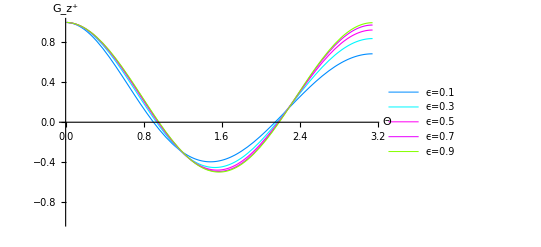

```mathematica
PlotORF[PTAPlus,{0.1,0.3,0.5,0.7,0.9},"G_z^+"]
```

## PTA S Function

```mathematica
PTAScalarIntegral[Θ_,ϵ_]:=NIntegrate[(Cos[Θ]^2 Sin[θ]^5)/(4 (1+(-1+ϵ) Cos[θ]) (1+(-1+ϵ) Cos[θ] Cos[Θ]+(-1+ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[θ] Cos[Θ] Cos[ϕ] Sin[θ]^4 Sin[Θ])/(2 (1+(-1+ϵ) Cos[θ]) (1+(-1+ϵ) Cos[θ] Cos[Θ]+(-1+ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^3 Sin[Θ]^2)/(4 (1+(-1+ϵ) Cos[θ]) (1+(-1+ϵ) Cos[θ] Cos[Θ]+(-1+ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Sin[θ]^3 Sin[Θ]^2 Sin[ϕ]^2)/(4 (1+(-1+ϵ) Cos[θ]) (1+(-1+ϵ) Cos[θ] Cos[Θ]+(-1+ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
PTAScalar[Θ_,ϵ_]=π/3((4+10 ϵ-5 ϵ^2)-2(1+10 ϵ-5 ϵ^2) Sin[Θ/2]^2)/(1-ϵ)^4-2π(ϵ(2-ϵ)(1-Sin[Θ/2]^2))/(1-ϵ)^5 Log[(2-ϵ)/ϵ]+π(ϵ^2(2-ϵ)^2)/((1-ϵ)^5 Sin[Θ/2] √(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2))Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ)Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

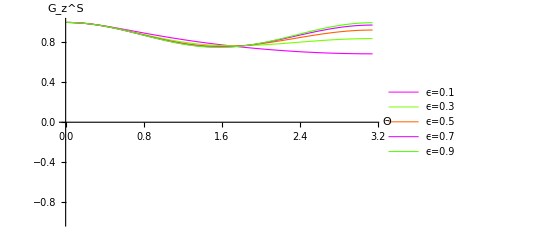

```mathematica
PlotORF[PTAScalar,{0.1,0.3,0.5,0.7,0.9},"G_z^S"]
```

## PTA X Function

```mathematica
PTAXIntegral[Θ_,ϵ_]:=NIntegrate[(Cos[θ]^2 Cos[Θ]^2 Sin[θ]^3)/((1+(-1+ϵ) Cos[θ]) (1+(-1+ϵ) Cos[θ] Cos[Θ]+(-1+ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[θ]^3 Cos[Θ] Cos[ϕ] Sin[θ]^2 Sin[Θ])/((1+(-1+ϵ) Cos[θ]) (1+(-1+ϵ) Cos[θ] Cos[Θ]+(-1+ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[θ] Cos[Θ] Cos[ϕ] Sin[θ]^4 Sin[Θ])/((1+(-1+ϵ) Cos[θ]) (1+(-1+ϵ) Cos[θ] Cos[Θ]+(-1+ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^3 Sin[Θ]^2)/((1+(-1+ϵ) Cos[θ]) (1+(-1+ϵ) Cos[θ] Cos[Θ]+(-1+ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
PTAX[Θ_,ϵ_]=-(4 π)/3((7+4 ϵ-2 ϵ^2)-4 (2+2 ϵ-ϵ^2) Sin[Θ/2]^2)/(1-ϵ)^4+4 π ((1+2 ϵ-ϵ^2)-2ϵ(2 -ϵ) Sin[Θ/2]^2)/(1-ϵ)^5 Log[(2-ϵ)/ϵ]-4π(ϵ(2 -ϵ)+2(1-ϵ)^2 Sin[Θ/2]^2)/((1-ϵ)^5 Sin[Θ/2] √(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2))Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ)Sin[Θ/2])/(√(ϵ(2 -ϵ)))];
```

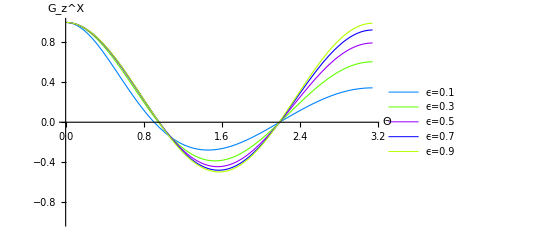

```mathematica
PlotORF[PTAX,{0.1,0.3,0.5,0.7,0.9},"G_z^X"]
```

## PTA L Function

```mathematica
PTALongIntegral[Θ_,ϵ_]:=NIntegrate[(Cos[θ]^4 Cos[Θ]^2 Sin[θ])/(2 (1+(-1+ϵ) Cos[θ]) (1+(-1+ϵ) Cos[θ] Cos[Θ]+(-1+ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[θ]^3 Cos[Θ] Cos[ϕ] Sin[θ]^2 Sin[Θ])/((1+(-1+ϵ) Cos[θ]) (1+(-1+ϵ) Cos[θ] Cos[Θ]+(-1+ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^3 Sin[Θ]^2)/(2 (1+(-1+ϵ) Cos[θ]) (1+(-1+ϵ) Cos[θ] Cos[Θ]+(-1+ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
PTALong[Θ_,ϵ_]=(2 π)/3((10-2ϵ+ϵ^2)-2(7-2ϵ+ϵ^2)Sin[Θ/2]^2)/(1-ϵ)^4-4 π(1-Sin[Θ/2]^2)/(1-ϵ)^5 Log[(2-ϵ)/ϵ]+2π 1/((1-ϵ)^5 Sin[Θ/2] √(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)) Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ) Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

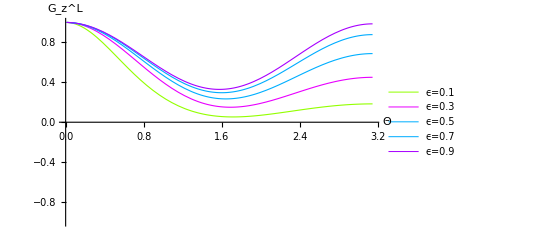

```mathematica
PlotORF[PTALong,{0.1,0.3,0.5,0.7,0.9},"G_z^L"]
```

## Astrometric Functions

## Astrometric + xθ Function

```mathematica
AstroPlusxθIntegral[Θ_,ϵ_]:=NIntegrate[((1-ϵ)^2 Cos[Θ] Cos[ϕ]^2 Sin[θ]^3)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[θ] Cos[Θ] Cos[ϕ]^2 Sin[θ]^3)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[2 Θ] Cos[ϕ]^2 Sin[θ]^2 Sin[2 θ])/(8 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[θ] Cos[2 Θ] Cos[ϕ]^2 Sin[θ]^2 Sin[2 θ])/(8 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ)^2 Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[Θ])/(8 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ) Cos[θ]^2 Cos[ϕ] Sin[θ]^2 Sin[Θ])/(8 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ)^2 Cos[θ] Cos[3 ϕ] Sin[θ]^2 Sin[Θ])/(8 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ) Cos[θ]^2 Cos[3 ϕ] Sin[θ]^2 Sin[Θ])/(8 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(7 (1-ϵ) Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 Θ])/(64 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(7 Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 Θ])/(64 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ) Cos[2 θ] Cos[3 ϕ] Sin[θ]^2 Sin[2 Θ])/(64 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[θ] Cos[2 θ] Cos[3 ϕ] Sin[θ]^2 Sin[2 Θ])/(64 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(3 (1-ϵ) Sin[θ]^2 Sin[2 Θ] Sin[ϕ] Sin[2 ϕ])/(32 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(3 Cos[θ] Sin[θ]^2 Sin[2 Θ] Sin[ϕ] Sin[2 ϕ])/(32 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
AstroPlusxθ[Θ_,ϵ_]=π/3((7-26 ϵ+13 ϵ^2)-2 (7-20 ϵ+10 ϵ^2) Sin[Θ/2]^2)/(1-ϵ)^4-π/4((1-ϵ)^2 (2-ϵ)^3-2(2-ϵ)^2(3-8 ϵ+9 ϵ^2-2 ϵ^3)Sin[Θ/2]^2+2 (2-ϵ) (6-23 ϵ+36 ϵ^2-18 ϵ^3+2 ϵ^4)Sin[Θ/2]^4-4 (4-12 ϵ+18 ϵ^2-12 ϵ^3+3 ϵ^4) Sin[Θ/2]^6)/((1-ϵ)^5 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[2-ϵ]+π/4(ϵ^3(1-ϵ)^2 -2 ϵ^2 (7-4 ϵ-3 ϵ^2+2 ϵ^3) Sin[Θ/2]^2-2 ϵ (8-31 ϵ+24 ϵ^2-2 ϵ^3-2 ϵ^4) Sin[Θ/2]^4-4 (4-12 ϵ+18 ϵ^2-12 ϵ^3+3 ϵ^4)Sin[Θ/2]^6)/((1-ϵ)^5 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[ϵ]+π/4((2-ϵ-2 Sin[Θ/2]^2)(2-ϵ-2(1-ϵ)Sin[Θ/2]^2)^2)/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[2-ϵ-2(1-ϵ) Sin[Θ/2]^2]-π/4((ϵ-2 Sin[Θ/2]^2) (ϵ+2(1-ϵ) Sin[Θ/2]^2)^2)/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[ϵ+2(1-ϵ) Sin[Θ/2]^2]-π(( ϵ^2(2-ϵ)^2+8 ϵ(2-ϵ)(1-ϵ)^2 Sin[Θ/2]^2+8 (1-ϵ)^4 Sin[Θ/2]^4)Sin[Θ/2])/((1-ϵ)^5(1- Sin[Θ/2]^2)√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2))Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ)Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

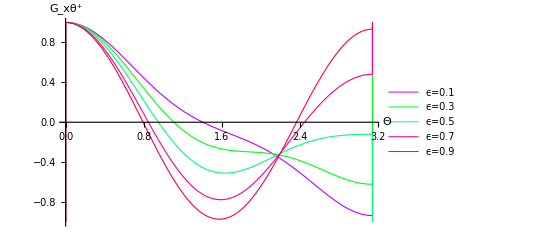

```mathematica
PlotORF[AstroPlusxθ,{0.1,0.3,0.5,0.7,0.9},"G_xθ^+"]
```

## Astrometric + yϕ Function

```mathematica
AstroPlusyϕIntegral[Θ_,ϵ_]:=NIntegrate[-(((1-ϵ) Cos[θ] Cos[Θ] Sin[θ]^3 Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])))+(Cos[θ]^2 Cos[Θ] Sin[θ]^3 Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ)^2 Cos[2 Θ] Sin[θ]^3 Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[θ] Cos[2 Θ] Sin[θ]^3 Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(3 (1-ϵ) Cos[ϕ] Sin[θ]^2 Sin[Θ] Sin[ϕ]^2)/(8 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(3 Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[Θ] Sin[ϕ]^2)/(8 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ) Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[Θ] Sin[ϕ]^2)/(8 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[Θ] Sin[ϕ]^2)/(8 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ)^2 Cos[θ] Cos[Θ] Cos[ϕ] Sin[θ]^2 Sin[Θ] Sin[ϕ]^2)/(2 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ) Cos[θ]^2 Cos[Θ] Cos[ϕ] Sin[θ]^2 Sin[Θ] Sin[ϕ]^2)/(2 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
AstroPlusyϕ[Θ_,ϵ_]=-π/3((5-10 ϵ+17 ϵ^2-12 ϵ^3+3 ϵ^4)+6ϵ(2-ϵ) (1-ϵ)^2 Sin[Θ/2]^2)/(1-ϵ)^4 +π/4 1/((1-ϵ)^5 Sin[Θ/2]^2(1-Sin[Θ/2]^2))((2-ϵ)^3 (1-ϵ)^2-2 (2-ϵ)^2 (3-9 ϵ+7 ϵ^2-3 ϵ^3)Sin[Θ/2]^2+2(2-ϵ)(6-15 ϵ+16 ϵ^2-14 ϵ^3+6 ϵ^4)Sin[Θ/2]^4-4 ϵ^2(1-ϵ)^2 (3-2 ϵ)Sin[Θ/2]^6)Log[2-ϵ]-π/4 1/((1-ϵ)^5 Sin[Θ/2]^2(1-Sin[Θ/2]^2))(ϵ^3(1-ϵ)^2+2 ϵ^2 (11-17 ϵ+11 ϵ^2-3 ϵ^3)Sin[Θ/2]^2+2 ϵ (24-73 ϵ+76 ϵ^2-34 ϵ^3+6 ϵ^4)Sin[Θ/2]^4 +4(1-2 ϵ) (2-ϵ)^2(1-ϵ)^2 Sin[Θ/2]^6) Log[ϵ]+π/4((ϵ+2(1-ϵ)Sin[Θ/2]^2)^3)/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[ϵ+2(1-ϵ)Sin[Θ/2]^2]-π/4((2-ϵ-2(1-ϵ)Sin[Θ/2]^2)^3)/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[2-ϵ-2(1-ϵ)Sin[Θ/2]^2]-π((ϵ^2(2-ϵ)^2+8 ϵ(2-ϵ) (1-ϵ)^2 Sin[Θ/2]^2+8 (1-ϵ)^4 Sin[Θ/2]^4 )√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2))/((1-ϵ)^5 Sin[Θ/2](1-Sin[Θ/2]^2))Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ) Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

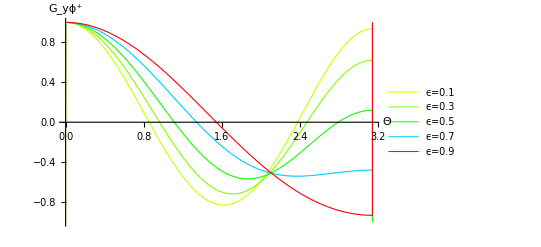

```mathematica
PlotORF[AstroPlusyϕ,{0.1,0.3,0.5,0.7,0.9},"G_yϕ^+"]
```

## Astrometric × xθ Function

```mathematica
AstroCrossxθIntegral[Θ_,ϵ_]:=NIntegrate[((1-ϵ) Cos[θ] Cos[Θ] Sin[θ]^3 Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[2 Θ] Sin[θ]^3 Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(3 (1-ϵ) Cos[ϕ] Sin[θ]^2 Sin[Θ] Sin[ϕ]^2)/(8 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[Θ] Sin[ϕ]^2)/(8 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[θ] Cos[Θ] Cos[ϕ] Sin[θ]^2 Sin[Θ] Sin[ϕ]^2)/(2 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
AstroCrossxθ[Θ_,ϵ_]=-π/3 (5-4 ϵ+2 ϵ^2)/(1-ϵ)^2+π/4 ((2-ϵ)^2 ((2-ϵ)-2(3-2ϵ)Sin[Θ/2]^2+2(3-2 ϵ)Sin[Θ/2]^4))/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[2-ϵ]-π/4(ϵ^2(ϵ+2(1-2 ϵ)Sin[Θ/2]^2-2(1-2 ϵ)Sin[Θ/2]^4))/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[ϵ]-π/4((2-ϵ-2 Sin[Θ/2]^2)(2-ϵ-2(1-ϵ)Sin[Θ/2]^2)^2)/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[2-ϵ-2(1-ϵ) Sin[Θ/2]^2]+π/4((ϵ-2 Sin[Θ/2]^2) (ϵ+2(1-ϵ) Sin[Θ/2]^2)^2)/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[ϵ+2(1-ϵ) Sin[Θ/2]^2];
```

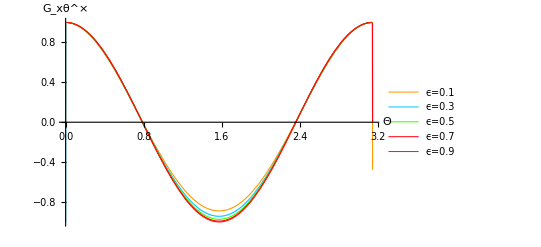

```mathematica
PlotORF[AstroCrossxθ,{0.1,0.3,0.5,0.7,0.9},"G_xθ^×"]
```

## Astrometric × yϕ Function

```mathematica
AstroCrossyϕIntegral[Θ_,ϵ_]:=NIntegrate[-((Cos[Θ] Cos[ϕ]^2 Sin[θ]^3)/(4 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])))+((1-ϵ) Cos[2 Θ] Cos[ϕ]^2 Sin[θ]^2 Sin[2 θ])/(8 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[θ] Cos[ϕ] Cos[2 ϕ] Sin[θ]^2 Sin[Θ])/(4 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(3 (1-ϵ) Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[2 Θ])/(32 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[2 θ] Cos[ϕ] Cos[2 ϕ] Sin[θ]^2 Sin[2 Θ])/(32 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(3 (1-ϵ) Cos[ϕ] Sin[θ]^2 Sin[2 Θ] Sin[ϕ]^2)/(16 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
AstroCrossyϕ[Θ_,ϵ_]=π/3((7-8 ϵ+4 ϵ^2)(1-2 Sin[Θ/2]^2))/(1-ϵ)^2-π/4((2-ϵ)^2((2-ϵ)-6(1-ϵ)Sin[Θ/2]^2+6(1-2ϵ)Sin[Θ/2]^4 -4(1-2 ϵ)Sin[Θ/2]^6))/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[2-ϵ]+π/4 (ϵ^2(ϵ+6(1-ϵ)Sin[Θ/2]^2-6(3-2ϵ)Sin[Θ/2]^4+4(3-2 ϵ)Sin[Θ/2]^6))/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[ϵ]+π/4((2-ϵ-2(1-ϵ)Sin[Θ/2]^2)^3)/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2)) Log[2-ϵ-2(1-ϵ)Sin[Θ/2]^2]-π/4((ϵ+2(1-ϵ) Sin[Θ/2]^2)^3)/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2)) Log[ϵ+2(1-ϵ) Sin[Θ/2]^2];
```

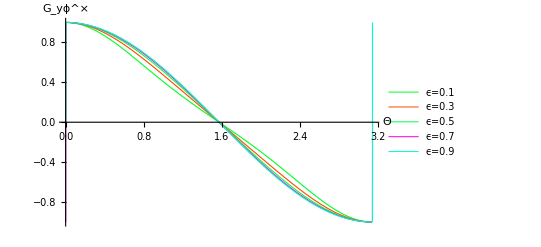

```mathematica
PlotORF[AstroCrossyϕ,{0.1,0.3,0.5,0.7,0.9},"G_yϕ^×"]
```

## Astrometric Tensorial xθ Function

```mathematica
AstroTensorialxθ[Θ_,ϵ_]=(2π)/3 ((1-6 ϵ-ϵ^2+4 ϵ^3-ϵ^4)-(7-20 ϵ+10 ϵ^2) Sin[Θ/2]^2)/(1-ϵ)^4+π/2(2 ϵ^2(2-ϵ)^2+ϵ(2-ϵ)(4-14 ϵ+7 ϵ^2) Sin[Θ/2]^2+2(4-12 ϵ+18 ϵ^2-12 ϵ^3+3 ϵ^4)Sin[Θ/2]^4)/((1-ϵ)^5(1-Sin[Θ/2]^2))Log[(2-ϵ)/ϵ]-π(( ϵ^2(2-ϵ)^2+8 ϵ(2-ϵ)(1-ϵ)^2 Sin[Θ/2]^2+8 (1-ϵ)^4 Sin[Θ/2]^4) Sin[Θ/2])/((1-ϵ)^5(1- Sin[Θ/2]^2)√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2))Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ) Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

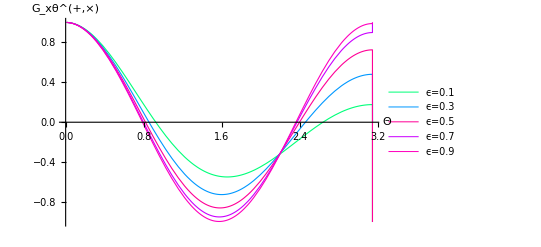

```mathematica
PlotORF[AstroTensorialxθ,{0.1,0.3,0.5,0.7,0.9},"G_xθ^(+,×)"]
```

## Astrometric Tensorial yϕ Function

```mathematica
AstroTensorialyϕ[Θ_,ϵ_]=π/3((2-12 ϵ+10 ϵ^2-4 ϵ^3+ϵ^4)-2(1-ϵ)^2(7-2 ϵ+ϵ^2)Sin[Θ/2]^2)/(1-ϵ)^4+π/2(2 ϵ^2(2-ϵ)^2+ϵ(2-ϵ)(12-26 ϵ+13 ϵ^2)Sin[Θ/2]^2+4(1-ϵ)^2 (2-6 ϵ+3 ϵ^2)Sin[Θ/2]^4)/((1-ϵ)^5(1-Sin[Θ/2]^2))Log[(2-ϵ)/ϵ]-π((ϵ^2(2-ϵ)^2+8 ϵ(2-ϵ) (1-ϵ)^2 Sin[Θ/2]^2+8 (1-ϵ)^4 Sin[Θ/2]^4 )√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2))/((1-ϵ)^5 Sin[Θ/2](1-Sin[Θ/2]^2))Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ) Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

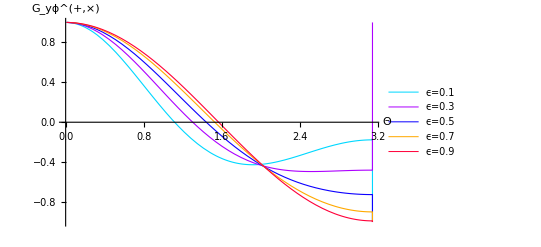

```mathematica
PlotORF[AstroTensorialyϕ,{0.1,0.3,0.5,0.7,0.9},"G_yϕ^(+,×)"]
```

## Astrometric Scalar xθ Function

```mathematica
AstroScalarxθIntegral[Θ_,ϵ_]:=NIntegrate[((1-ϵ)^2 Cos[Θ] Cos[ϕ]^2 Sin[θ]^3)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[θ] Cos[Θ] Cos[ϕ]^2 Sin[θ]^3)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[θ] Cos[Θ]^2 Cos[ϕ]^2 Sin[θ]^3)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[θ]^2 Cos[Θ]^2 Cos[ϕ]^2 Sin[θ]^3)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ)^2 Cos[θ] Cos[ϕ] Sin[θ]^2 Sin[Θ])/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ) Cos[θ]^2 Cos[ϕ] Sin[θ]^2 Sin[Θ])/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ) Cos[θ]^2 Cos[Θ] Cos[ϕ] Sin[θ]^2 Sin[Θ])/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[θ]^3 Cos[Θ] Cos[ϕ] Sin[θ]^2 Sin[Θ])/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[Θ] Cos[ϕ]^3 Sin[θ]^4 Sin[Θ])/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[θ] Cos[Θ] Cos[ϕ]^3 Sin[θ]^4 Sin[Θ])/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ) Cos[θ] Cos[ϕ]^2 Sin[θ]^3 Sin[Θ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[θ]^2 Cos[ϕ]^2 Sin[θ]^3 Sin[Θ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
AstroScalarxθ[Θ_,ϵ_]=π/3((1-8 ϵ-8 ϵ^2+12 ϵ^3-3 ϵ^4)-2 (1-8 ϵ+4 ϵ^2) Sin[Θ/2]^2)/(1-ϵ)^4+π/2(ϵ^2(2-ϵ)^2(2-3 Sin[Θ/2]^2+2 Sin[Θ/2]^4))/((1-ϵ)^5 (1-Sin[Θ/2]^2)) Log[(2-ϵ)/ϵ]-π(ϵ^2(2-ϵ)^2 Sin[Θ/2])/((1-ϵ)^5 (1-Sin[Θ/2]^2)√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2))Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ)Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

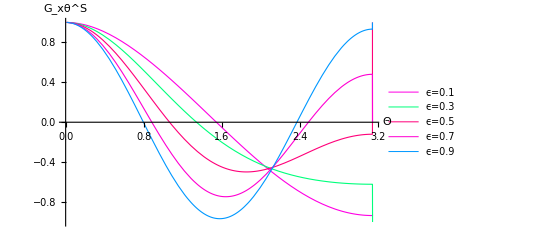

```mathematica
PlotORF[AstroScalarxθ,{0.1,0.3,0.5,0.7,0.9},"G_xθ^S"]
```

## Astrometric Scalar yϕ Function

```mathematica
AstroScalaryϕIntegral[Θ_,ϵ_]:=NIntegrate[((1-ϵ)^2 Sin[θ]^3 Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[θ] Sin[θ]^3 Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[θ] Cos[Θ] Sin[θ]^3 Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[θ]^2 Cos[Θ] Sin[θ]^3 Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[ϕ] Sin[θ]^4 Sin[Θ] Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[θ] Cos[ϕ] Sin[θ]^4 Sin[Θ] Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
AstroScalaryϕ[Θ_,ϵ_]=π/3(1-8 ϵ+4 ϵ^2)/(1-ϵ)^4+π/2(ϵ^2(2-ϵ)^2(2-Sin[Θ/2]^2))/((1-ϵ)^5 (1-Sin[Θ/2]^2)) Log[(2-ϵ)/ϵ]-π (ϵ^2(2-ϵ)^2 √(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2))/((1-ϵ)^5 Sin[Θ/2](1-Sin[Θ/2]^2))Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ)Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

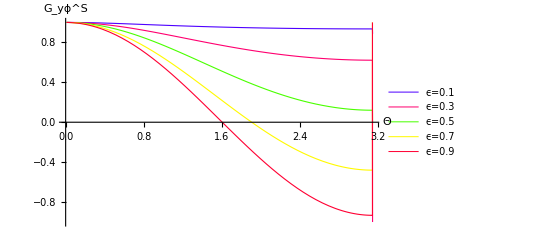

```mathematica
PlotORF[AstroScalaryϕ,{0.1,0.3,0.5,0.7,0.9},"G_yϕ^S"]
```

## Astrometric X xθ Function

```mathematica
AstroXxθIntegral[Θ_,ϵ_]:=NIntegrate[((1-ϵ)^2 Cos[θ]^2 Cos[Θ] Cos[ϕ]^2 Sin[θ])/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[θ] Cos[2 θ] Cos[Θ] Cos[ϕ]^2 Sin[θ])/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[θ] Cos[2 θ] Cos[2 Θ] Cos[ϕ]^2 Sin[θ])/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[2 θ]^2 Cos[2 Θ] Cos[ϕ]^2 Sin[θ])/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ)^2 Cos[θ] Cos[ϕ]^3 Sin[θ]^2 Sin[Θ])/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[2 θ] Cos[ϕ]^3 Sin[θ]^2 Sin[Θ])/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(3 (1-ϵ) Cos[θ] Cos[ϕ] Sin[θ] Sin[2 θ] Sin[2 Θ])/(16 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(3 Cos[2 θ] Cos[ϕ] Sin[θ] Sin[2 θ] Sin[2 Θ])/(16 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[θ] Cos[ϕ] Cos[2 ϕ] Sin[θ] Sin[2 θ] Sin[2 Θ])/(16 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[2 θ] Cos[ϕ] Cos[2 ϕ] Sin[θ] Sin[2 θ] Sin[2 Θ])/(16 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
AstroXxθ[Θ_,ϵ_]=π/6((1+88 ϵ-32 ϵ^2-12 ϵ^3+3 ϵ^4)+16(1-8 ϵ+4 ϵ^2)Sin[Θ/2]^2)/(1-ϵ)^4+π/4((2-ϵ)^2 (1-ϵ)^2-2(4+15 ϵ^2-14 ϵ^3+3 ϵ^4)Sin[Θ/2]^2-2(4-24 ϵ-3 ϵ^2+14 ϵ^3-3 ϵ^4)Sin[Θ/2]^4-16ϵ (2-ϵ)Sin[Θ/2]^6)/((1-ϵ)^5 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[2-ϵ]-π/4(ϵ^2(1-ϵ)^2-2 ϵ (12+3 ϵ-10 ϵ^2+3 ϵ^3)Sin[Θ/2]^2-2 (8-36 ϵ+9 ϵ^2+10 ϵ^3-3 ϵ^4)Sin[Θ/2]^4 -16 ϵ(2-ϵ)Sin[Θ/2]^6)/((1-ϵ)^5 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[ϵ]-π/4((2-ϵ)^2-2(2-ϵ)^2 Sin[Θ/2]^2+4(1-ϵ)Sin[Θ/2]^4)/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2)) Log[2-ϵ-2(1-ϵ)Sin[Θ/2]^2]+π/4(ϵ^2-2 ϵ^2 Sin[Θ/2]^2 -4 (1-ϵ)Sin[Θ/2]^4)/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2)) Log[ϵ+2(1-ϵ)Sin[Θ/2]^2]+4 π ((ϵ(2-ϵ)+2 (1-ϵ)^2 Sin[Θ/2]^2)Sin[Θ/2])/((1-ϵ)^5 (1-Sin[Θ/2]^2)√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2))Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ) Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

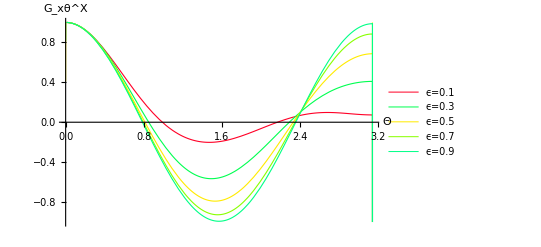

```mathematica
PlotORF[AstroXxθ,{0.1,0.3,0.5,0.7,0.9},"G_xθ^X"]
```

## Astrometric X yϕ Function

```mathematica
AstroXyϕIntegral[Θ_,ϵ_]:=NIntegrate[-(((1-ϵ) Cos[θ]^3 Cos[Θ] Sin[θ] Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])))+(Cos[θ]^2 Cos[2 θ] Cos[Θ] Sin[θ] Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ)^2 Cos[θ]^2 Cos[Θ]^2 Sin[θ] Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[θ] Cos[2 θ] Cos[Θ]^2 Sin[θ] Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ) Cos[θ] Cos[Θ] Sin[θ]^3 Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[2 θ] Cos[Θ] Sin[θ]^3 Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[θ]^2 Cos[ϕ] Sin[θ]^2 Sin[Θ] Sin[ϕ]^2)/(2 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[θ] Cos[2 θ] Cos[ϕ] Sin[θ]^2 Sin[Θ] Sin[ϕ]^2)/(2 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ)^2 Cos[θ] Cos[Θ] Cos[ϕ] Sin[θ]^2 Sin[Θ] Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[2 θ] Cos[Θ] Cos[ϕ] Sin[θ]^2 Sin[Θ] Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
AstroXyϕ[Θ_,ϵ_]= π/6((13+16 ϵ+4 ϵ^2-12 ϵ^3+3 ϵ^4)+6 (1-ϵ)^2 (1+2 ϵ-ϵ^2)Sin[Θ/2]^2)/(1-ϵ)^4-π/4 ((2-ϵ)^2(1-ϵ)^2-4(2-ϵ) (1-6 ϵ+ϵ^2)Sin[Θ/2]^2+2(8-18 ϵ-3 ϵ^2+12 ϵ^3-3 ϵ^4)Sin[Θ/2]^4-4ϵ (2-ϵ) (1-ϵ)^2 Sin[Θ/2]^6)/((1-ϵ)^5 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[2-ϵ]+π/4(ϵ^2 (1-ϵ)^2+4 ϵ (7-2 ϵ-ϵ^2)Sin[Θ/2]^2+2(8-18 ϵ-3 ϵ^2+12 ϵ^3-3 ϵ^4)Sin[Θ/2]^4-4ϵ(2-ϵ)(1-ϵ)^2 Sin[Θ/2]^6)/((1-ϵ)^5 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[ϵ]+π/4 ((2-ϵ-2(1-ϵ)Sin[Θ/2]^2)^2)/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2)) Log[2-ϵ-2(1-ϵ)Sin[Θ/2]^2]-π/4((ϵ+2(1-ϵ) Sin[Θ/2]^2)^2)/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2)) Log[ϵ+2(1-ϵ) Sin[Θ/2]^2]+4π((ϵ (2-ϵ)+2(1-ϵ)^2 Sin[Θ/2]^2)√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2))/((1-ϵ)^5 Sin[Θ/2](1-Sin[Θ/2]^2))Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ)Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

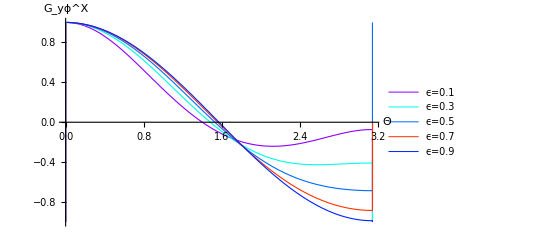

```mathematica
PlotORF[AstroXyϕ,{0.1,0.3,0.5,0.7,0.9},"G_yϕ^X"]
```

## Astrometric Y xθ Function

```mathematica
AstroYxθIntegral[Θ_,ϵ_]:=NIntegrate[((1-ϵ) Cos[θ]^3 Cos[Θ] Sin[θ] Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[θ]^2 Cos[2 Θ] Sin[θ] Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ) Cos[θ]^2 Cos[ϕ] Sin[θ]^2 Sin[Θ] Sin[ϕ]^2)/(4 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[θ] Cos[Θ] Cos[ϕ] Sin[θ]^2 Sin[Θ] Sin[ϕ]^2)/(2 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
AstroYxθ[Θ_,ϵ_]=π/6 (7-2 ϵ+ϵ^2)/(1-ϵ)^2-π/4((2-ϵ)^2(1-2 Sin[Θ/2]^2+2 Sin[Θ/2]^4))/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2)) Log[2-ϵ]+π/4(ϵ^2(1-2 Sin[Θ/2]^2+2 Sin[Θ/2]^4))/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[ϵ]+π/4((2-ϵ)^2-2(2-ϵ)^2 Sin[Θ/2]^2+4(1-ϵ)Sin[Θ/2]^4)/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[2-ϵ-2(1-ϵ)Sin[Θ/2]^2]-π/4(ϵ^2-2 ϵ^2 Sin[Θ/2]^2-4(1- ϵ)Sin[Θ/2]^4)/((1-ϵ)^3 Sin[Θ/2]^2(1-Sin[Θ/2]^2))Log[ϵ+2(1-ϵ) Sin[Θ/2]^2];
```

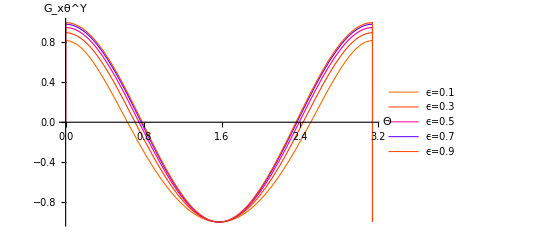

```mathematica
PlotORF[AstroYxθ,{0.1,0.3,0.5,0.7,0.9},"G_xθ^Y"]
```

## Astrometric Y yϕ Function

```mathematica
AstroYyϕIntegral[Θ_,ϵ_]:=NIntegrate[((1-ϵ) Cos[θ] Cos[ϕ]^2 Sin[θ])/(8 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[θ]^2 Cos[Θ] Cos[ϕ]^2 Sin[θ])/(4 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ) Cos[θ] Cos[2 θ] Cos[2 Θ] Cos[ϕ]^2 Sin[θ])/(8 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[θ] Cos[ϕ] Cos[2 ϕ] Sin[θ]^2 Sin[Θ])/(4 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(3 (1-ϵ) Cos[θ] Cos[ϕ] Sin[θ] Sin[2 θ] Sin[2 Θ])/(32 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ) Cos[θ] Cos[ϕ] Cos[2 ϕ] Sin[θ] Sin[2 θ] Sin[2 Θ])/(32 (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
AstroYyϕ[Θ_,ϵ_]=-π/6((5+2 ϵ-ϵ^2)(1-2 Sin[Θ/2]^2))/(1-ϵ)^2+π((2-ϵ)((2-ϵ)-4(1-ϵ)Sin[Θ/2]^2 -6ϵ Sin[Θ/2]^4 +4ϵ Sin[Θ/2]^6 ))/((1-ϵ)^3 Sin[Θ]^2)Log[2-ϵ]-π(ϵ( ϵ+4(1-ϵ)Sin[Θ/2]^2-6(2-ϵ)Sin[Θ/2]^4+4(2-ϵ)Sin[Θ/2]^6))/((1-ϵ)^3 Sin[Θ]^2)Log[ϵ]-π((2-ϵ-2(1-ϵ)Sin[Θ/2]^2)^2)/((1-ϵ)^3 Sin[Θ]^2)Log[2-ϵ-2(1-ϵ)Sin[Θ/2]^2]+π ((ϵ+2(1-ϵ) Sin[Θ/2]^2)^2)/((1-ϵ)^3 Sin[Θ]^2)Log[ϵ+2(1-ϵ) Sin[Θ/2]^2];
```

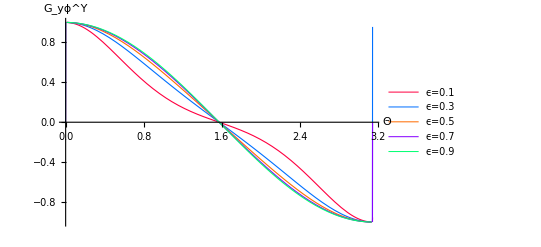

```mathematica
PlotORF[AstroYyϕ,{0.1,0.3,0.5,0.7,0.9},"G_yϕ^Y"]
```

## Astrometric Vectorial xθ Function

```mathematica
AstroVectorialxθ[Θ_,ϵ_]=(2π)/3((2+18 ϵ-5 ϵ^2-4 ϵ^3+ϵ^4)+4(1-8 ϵ+4 ϵ^2)Sin[Θ/2]^2)/(1-ϵ)^4-π(ϵ(6+ϵ-4 ϵ^2+ϵ^3)+(4-18 ϵ+5 ϵ^2+4 ϵ^3-ϵ^4)Sin[Θ/2]^2+4ϵ (2-ϵ)Sin[Θ/2]^4)/((1-ϵ)^5(1-Sin[Θ/2]^2))Log[(2-ϵ)/ϵ]+4 π ((ϵ(2-ϵ)+2 (1-ϵ)^2 Sin[Θ/2]^2)Sin[Θ/2])/((1-ϵ)^5(1-Sin[Θ/2]^2)√(1-(1-ϵ)^2 (1-Sin[Θ/2]^2)))Log[(√(1-(1-ϵ)^2 (1-Sin[Θ/2]^2))+(1-ϵ) Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

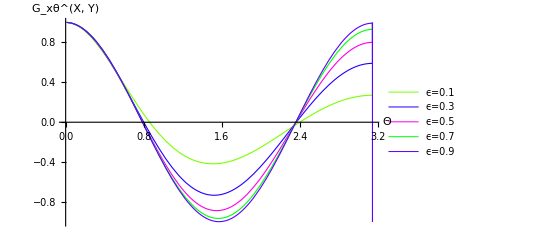

```mathematica
PlotORF[AstroVectorialxθ,{0.1,0.3,0.5,0.7,0.9},"G_xθ^(X, Y)"]
```

## Astrometric Vectorial yϕ Function

```mathematica
AstroVectorialyϕ[Θ_,ϵ_]= (2π)/3((2+6 ϵ+ϵ^2-4 ϵ^3+ϵ^4)+2(1-ϵ)^2 (2+2 ϵ-ϵ^2)Sin[Θ/2]^2)/(1-ϵ)^4-π (ϵ (1+ϵ)(3-ϵ) (2-ϵ)+(4-6 ϵ-9 ϵ^2+12 ϵ^3-3 ϵ^4)Sin[Θ/2]^2-2ϵ(2-ϵ) (1-ϵ)^2 Sin[Θ/2]^4)/((1-ϵ)^5(1-Sin[Θ/2]^2))Log[(2-ϵ)/ϵ]+4π((ϵ (2-ϵ)+2(1-ϵ)^2 Sin[Θ/2]^2)√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2))/((1-ϵ)^5 Sin[Θ/2](1-Sin[Θ/2]^2))Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ)Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

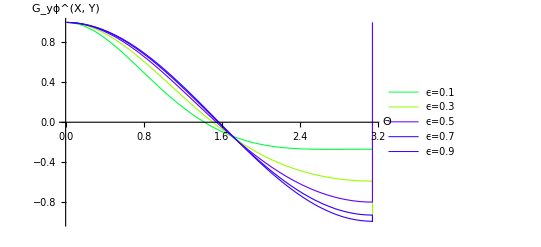

```mathematica
PlotORF[AstroVectorialyϕ,{0.1,0.3,0.5,0.7,0.9},"G_yϕ^(X, Y)"]
```

## Astrometric Longitudinal xθ Function

```mathematica
AstroLongxθIntegral[Θ_,ϵ_]:=NIntegrate[(Cos[θ]^2 Cos[2 Θ] Cos[ϕ]^2 Sin[θ]^3)/(2 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[θ]^3 Cos[Θ] Cos[ϕ] Sin[θ]^2 Sin[Θ])/(2 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[θ] Cos[Θ] Cos[ϕ]^3 Sin[θ]^4 Sin[Θ])/(2 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
AstroLongxθ[Θ_,ϵ_]=-(2π)/3 ((5+2 ϵ-ϵ^2)-2(2+2ϵ-ϵ^2)Sin[Θ/2]^2)/(1-ϵ)^4+π((1+2ϵ-ϵ^2)-3ϵ(2-ϵ)Sin[Θ/2]^2 +2ϵ(2-ϵ)Sin[Θ/2]^4)/((1-ϵ)^5(1-Sin[Θ/2]^2))Log[(2-ϵ)/ϵ]-2π Sin[Θ/2]/((1-ϵ)^5 (1-Sin[Θ/2]^2)√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2))Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ)Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

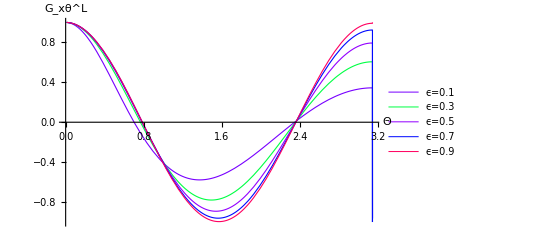

```mathematica
PlotORF[AstroLongxθ,{0.1,0.3,0.5,0.7,0.9},"G_xθ^L"]
```

## Astrometric Longitudinal yϕ Function

```mathematica
AstroLongyϕIntegral[Θ_,ϵ_]:=NIntegrate[(Cos[θ]^2 Cos[Θ] Sin[θ]^3 Sin[ϕ]^2)/(2 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[θ] Cos[ϕ] Sin[θ]^4 Sin[Θ] Sin[ϕ]^2)/(2 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
AstroLongyϕ[Θ_,ϵ_]=-(2π)/3(2+2 ϵ-ϵ^2)/(1-ϵ)^4+π((1+2 ϵ-ϵ^2)-ϵ(2-ϵ)Sin[Θ/2]^2)/((1-ϵ)^5(1-Sin[Θ/2]^2))Log[(2-ϵ)/ϵ]-2π(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2))/((1-ϵ)^5 Sin[Θ/2](1-Sin[Θ/2]^2))Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ)Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

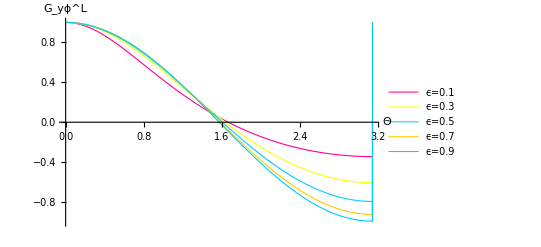

```mathematica
PlotORF[AstroLongyϕ,{0.1,0.3,0.5,0.7,0.9},"G_yϕ^L"]
```

## PTA-Astrometry Functions

## PTA-Astrometry + Function

```mathematica
PAPlusIntegral[Θ_,ϵ_]:=NIntegrate[-(((1-ϵ) Cos[Θ] Cos[ϕ] Sin[θ]^4)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])))+(Cos[θ] Cos[2 Θ] Cos[ϕ] Sin[θ]^4)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ) Cos[θ] Cos[2 ϕ] Sin[θ]^3 Sin[Θ])/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(3 Cos[Θ] Cos[2 ϕ] Sin[θ]^3 Sin[Θ])/(16 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[2 θ] Cos[Θ] Cos[2 ϕ] Sin[θ]^3 Sin[Θ])/(16 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(3 Sin[θ]^5 Sin[2 Θ])/(16 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
PAPlus[Θ_,ϵ_]=π/3((8-10 ϵ+5 ϵ^2)Sin[Θ/2] √(1-Sin[Θ/2]^2))/(1-ϵ)^4-π/2((2ϵ(4-6ϵ+4 ϵ^2-ϵ^3)+(8-24ϵ+24 ϵ^2-12 ϵ^3+3 ϵ^4)Sin[Θ/2]^2) Sin[Θ/2])/((1-ϵ)^5 √(1-Sin[Θ/2]^2))Log[(2-ϵ)/ϵ]+π(ϵ^2(2-ϵ)^2+8ϵ(2-ϵ) (1-ϵ)^2 Sin[Θ/2]^2+8 (1-ϵ)^4 Sin[Θ/2]^4)/((1-ϵ)^5 √(1-Sin[Θ/2]^2)√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2))Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ)Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

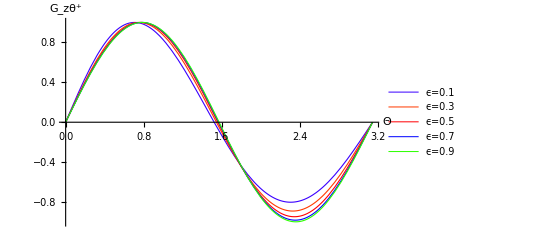

```mathematica
PlotORF[PAPlus,{0.1,0.3,0.5,0.7,0.9},"G_zθ^+"]
```

## PTA-Astrometry Scalar Function

```mathematica
PAScalarIntegral[Θ_,ϵ_]:=NIntegrate[-(((1-ϵ) Cos[Θ] Cos[ϕ] Sin[θ]^4)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])))+(Cos[θ] Cos[Θ]^2 Cos[ϕ] Sin[θ]^4)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+((1-ϵ) Cos[θ] Sin[θ]^3 Sin[Θ])/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[θ]^2 Cos[Θ] Sin[θ]^3 Sin[Θ])/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[Θ] Cos[ϕ]^2 Sin[θ]^5 Sin[Θ])/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[θ] Cos[ϕ] Sin[θ]^4 Sin[Θ]^2)/(4 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
PAScalar[Θ_,ϵ_]=π/3((2+2 ϵ-ϵ^2)Sin[Θ/2] √(1-Sin[Θ/2]^2))/(1-ϵ)^4-π/2(ϵ(2-ϵ)(2-(2-2ϵ+ϵ^2)Sin[Θ/2]^2)Sin[Θ/2])/((1-ϵ)^5 √(1-Sin[Θ/2]^2))Log[(2-ϵ)/ϵ]+π(ϵ^2(2-ϵ)^2)/((1-ϵ)^5 √(1-Sin[Θ/2]^2)√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2))Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ)Sin[Θ/2])/(√(ϵ(2-ϵ)))];
```

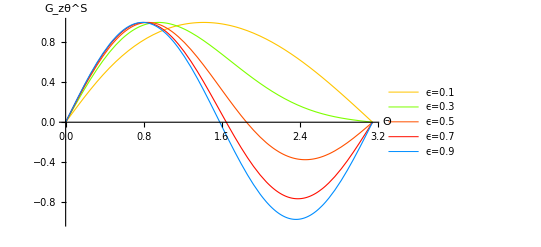

```mathematica
PlotORF[PAScalar,{0.1,0.3,0.5,0.7,0.9},"G_zθ^S"]
```

## PTA-Astrometry X Function

```mathematica
PAXIntegral[Θ_,ϵ_]:=NIntegrate[-(((1-ϵ) Cos[θ]^2 Cos[Θ] Cos[ϕ] Sin[θ]^2)/(2 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])))+(Cos[θ] Cos[2 θ] Cos[2 Θ] Cos[ϕ] Sin[θ]^2)/(2 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-((1-ϵ) Cos[θ] Cos[ϕ]^2 Sin[θ]^3 Sin[Θ])/(2 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(3 Cos[θ] Sin[θ]^2 Sin[2 θ] Sin[2 Θ])/(8 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))+(Cos[θ] Cos[2 ϕ] Sin[θ]^2 Sin[2 θ] Sin[2 Θ])/(8 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
PAX[Θ_,ϵ_]=-(4π)/3((5-4 ϵ+2 ϵ^2)Sin[Θ/2] √(1-Sin[Θ/2]^2))/(1-ϵ)^4+2π((2-ϵ(2-ϵ)Sin[Θ/2]^2)Sin[Θ/2])/((1-ϵ)^5 √(1-Sin[Θ/2]^2))Log[(2-ϵ)/ϵ]-4π(ϵ(2-ϵ)+2(1-ϵ)^2 Sin[Θ/2]^2)/((1-ϵ)^5 √(1-Sin[Θ/2]^2)√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)) Log[(√(ϵ(2-ϵ)+(1-ϵ)^2 Sin[Θ/2]^2)+(1-ϵ) Sin[Θ/2])/(√(1-(1-ϵ)^2))];
```

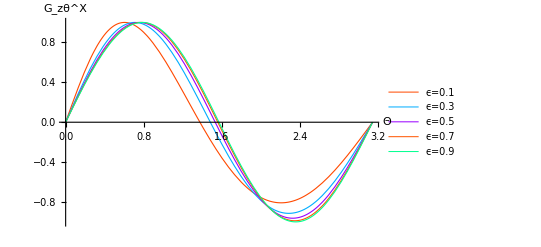

```mathematica
PlotORF[PAX,{0.1,0.3,0.5,0.7,0.9},"G_zθ^X"]
```

## PTA-Astrometry Longitudinal Function

```mathematica
PALongIntegral[Θ_,ϵ_]:=NIntegrate[-((Cos[θ]^3 Cos[2 Θ] Cos[ϕ] Sin[θ]^2)/(2 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])))+(Cos[θ]^4 Cos[Θ] Sin[θ] Sin[Θ])/(2 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ]))-(Cos[θ]^2 Cos[Θ] Cos[ϕ]^2 Sin[θ]^3 Sin[Θ])/(2 (-1+(1-ϵ) Cos[θ]) (-1+(1-ϵ) Cos[θ] Cos[Θ]+(1-ϵ) Cos[ϕ] Sin[θ] Sin[Θ])),{θ,0,π},{ϕ,0,2π}]
```

```mathematica
PALong[Θ_,ϵ_]=(2π)/3((5-4 ϵ+2 ϵ^2)Sin[Θ/2] √(1-Sin[Θ/2]^2))/(1-ϵ)^4-π(((3-2ϵ+ϵ^2)-(2-2ϵ+ϵ^2)Sin[Θ/2]^2)Sin[Θ/2])/((1-ϵ)^5 √(1-Sin[Θ/2]^2))Log[(2-ϵ)/ϵ]+2π 1/((1-ϵ)^5 √(1-Sin[Θ/2]^2)√(1-(1-ϵ)^2(1-Sin[Θ/2]^2)))Log[(√(1-(1-ϵ)^2(1-Sin[Θ/2]^2))+(1-ϵ)Sin[Θ/2])/(√(1-(1-ϵ)^2))];
```

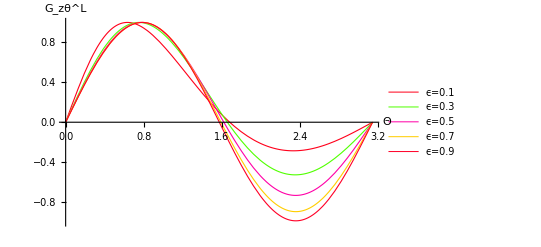

```mathematica
PlotORF[PALong,{0.1,0.3,0.5,0.7,0.9},"G_zθ^L"]
```